# 缠绕

### 使圆的半径随Sin变化

```mathematica
Manipulate[ParametricPlot[ReIm[Sin[k θ]Exp[I θ]],{θ,0,2π},PlotRange->1.5],{k,1,30,1}]
```

```mathematica
Manipulate[ParametricPlot[ReIm[(Sin[ω θ]+1)Exp[I θ k]],{θ,0,2π},PlotRange->3],{ω,0,30,1},{k,0,30,0}]
```

```mathematica
Manipulate[ParametricPlot[ReIm[(Power[ω θ,2]+1)Exp[I θ k]],{θ,0,2π},PlotRange->3],{ω,0,30,1},{k,0,30,0}]
```

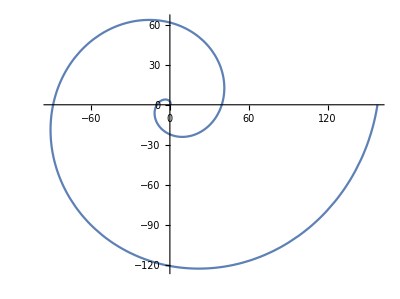

```mathematica
PolarPlot[x^2,{x,0,4π}]
```

```mathematica
ParametricPlot[ReIm[x^2 Exp[I x]],{x,0,4π}]
```

-Graphics-

```mathematica
Manipulate[ParametricPlot[ReIm[Sum[Sin[ω x],{ω,0,m,1}] Exp[I x k]],{x,0,4π}],{m,0,10,1},{k,0,10,1}]
```

```mathematica
Manipulate[Plot[Sum[Sin[ω x],{ω,0,m,1}],{x,0,4π}],{m,0,25,1}]
```